## Intro

### Constants

```mathematica
μBB=876;(*Baryon chemical potencial in MeV in case B*)

μI3B=-21.5;(*Izospin chemical potential in MeV in case B*)

TB=70.3;(*Temperature in MeV in casa B*)

HB=22.5;(*Hubble like constant of fireball expansion in MeV in case B*)

mp=938.27208816;(*Proton mass in MeV*)
mn=939.5654205;(*Neutron mass in MeV*)

RB=6.06 fm2MeV;(*Source fireball radius in MeV in case B*)

dB=0.4;(*Eccentricity in case B*)

Rt=1.7591 fm2MeV;(*Tritium radius in MeV*)
RHe3=1.963 fm2MeV; (*He3 radius in MeV*)
gs=2; (*Spin degeneration of nucleon*)

μpB=μBB+1/2 μI3B;(*Chemical potential of proton in MeV in case B*)

μnB=μBB-1/2 μI3B;(*Chemical potential of neutron in MeV in case B*)
fm2MeV = 1/197.3(*Conversion from fm to MeV*);
```

### Experimental data

```mathematica
SetDirectory[NotebookDirectory[]];
Protons = Import["protons.txt","Table"];
ProtonsY = Import["protonsY.txt","Table"];
Deuterons =Import["deuteronsmt2.txt","Table"];
DeuteronsY =Import["deuteronsY.txt","Table"];
Trytons = Import["trytons.txt","Table"];
TrytonsY = Import["trytonsY.txt","Table"];
He3 =Import["He3.txt","Table"];
He3Y=Import["He3Y3.txt","Table"];
```

### 4-vectors

```mathematica
vB[r_]:=Tanh[HB*r];(*Velocity in case B*)
gammaB[r_,θ_]:=(1-(1+dB Cos[2θ])Tanh[HB r ]^2)^(-1/2)(*Lorentz gamma in case B*)
g = ({{1, 0, 0, 0}, {0, -1, 0, 0}, {0, 0, -1, 0}, {0, 0, 0, -1}});(*metric*)
(*Velocity 4-vector in case B*)
uB[r_,ϕ_,θ_] := gammaB[r,θ]{1,√(1-dB)vB[r]Cos[ϕ]Sin[θ],√(1-dB)vB[r]Sin[ϕ]Sin[θ],√(1+dB)vB[r]Cos[θ]}
(*Momentum 4-vector*)
p[mt_,M_,y_,ϕp_]:={mt Cosh[y],√(mt^2 -M^2)Cos[ϕp],√(mt^2-M^2)Sin[ϕp],mt Sinh[y]}
```

### Formation ratios

```mathematica
(********************************************************************************************************)
```

```mathematica
(*Deuteron formation ratio in case B*)
H2AfrB = 942476.0;
(*Tritium formation rate in case B*)
H3AfrB=5.51*10^11;
(*He3 formation rate in case B*)
He3AfrB=5.03*10^11;
```

### Distribution function

```mathematica
(*Nucleon distribution function in case B*)
```

```mathematica
dNB[mt_,M_,μ_,y_]:=gs/(2π)^3 NIntegrate[(Exp[(p[mt,M,y,Qp].g.uB[r,Q,q]-μ)/TB]+1)^-1 r^2 Sin[q],{Q,0,2π},{q,0,π},{Qp,0,2π},{r,0,RB}]
```

## Protons

```mathematica
(*Proton distribution*)
```

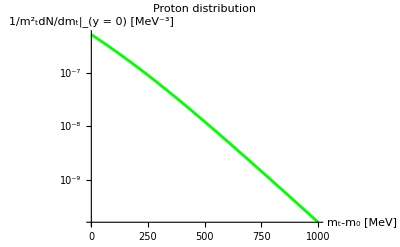

```mathematica
DistributionProtonB=LogPlot[{ dNB[mt+mp,mp,μpB,0]},{mt,0,1000},PlotStyle->Green,AxesLabel->{"m_t-m_0 [MeV]","1/((m^2)_t)dN/dm_t|_(y = 0) [MeV^-3]",Thick},PlotLabel->"Proton distribution",AxesStyle->Thick]
```

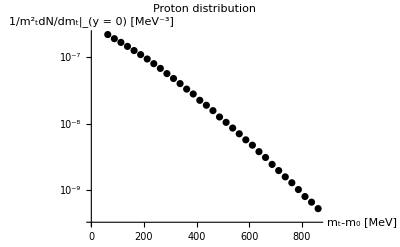

```mathematica
ProtonExpMt = ListLogPlot[Protons,PlotStyle->Black,AxesLabel->{"m_t-m_0 [MeV]","1/((m^2)_t)dN/dm_t|_(y = 0) [MeV^-3]"},PlotLabel->"Proton distribution",PlotStyle->Thick]
```

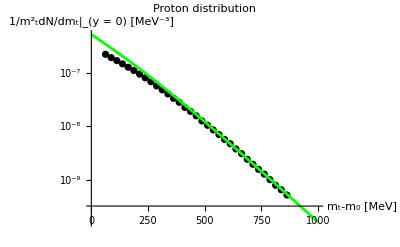

```mathematica
Show[ProtonExpMt,DistributionProtonB, PlotRange->All]
```

## Deuteron

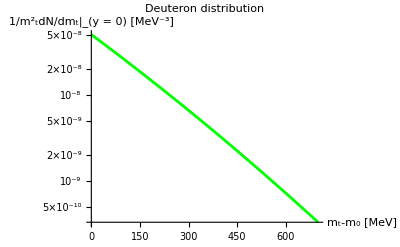

```mathematica
DistributionDeuteronB=LogPlot[{ H2AfrB/(2π)dNB[mt/2+mp,mp,μpB,0]dNB[mt/2+mn,mn,μnB,0]},{mt,0,700},PlotStyle->Green,AxesLabel->{"m_t-m_0 [MeV]","1/((m^2)_t)dN/dm_t|_(y = 0) [MeV^-3]",Thick},PlotLabel->"Deuteron distribution",AxesStyle->Thick]
```

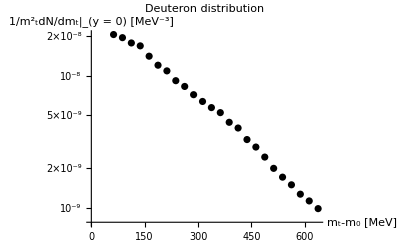

```mathematica
DeuteronExpMt = ListLogPlot[Deuterons,PlotStyle->Black,AxesLabel->{"m_t-m_0 [MeV]","1/((m^2)_t)dN/dm_t|_(y = 0) [MeV^-3]"},PlotLabel->"Deuteron distribution",PlotStyle->Thick]
```

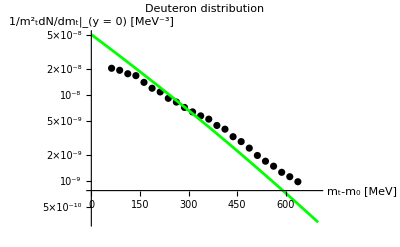

```mathematica
Show[DeuteronExpMt,DistributionDeuteronB, PlotRange->All]
```

## Tritium

### Transverse mass spectrum

```mathematica
(*Transverse mass tritium distribution in case B*)
```

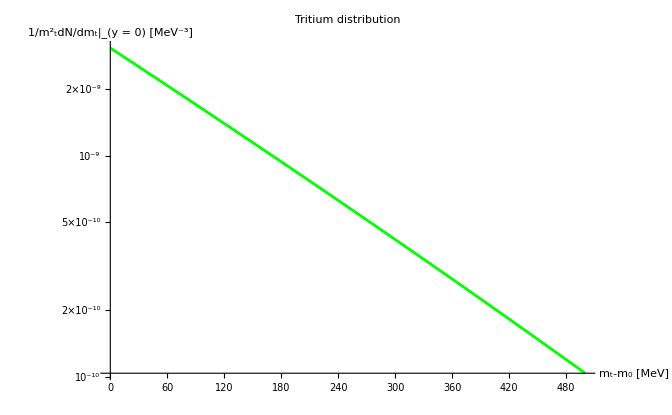

```mathematica
DistributionB=LogPlot[{H3AfrB/(2π)^2 dNB[mt/3+mp,mp,μpB,0]dNB[mt/3+mn,mn,μnB,0]dNB[mt/3+mn,mn,μnB,0]},{mt,0,500},PlotStyle->Red,AxesLabel->{"m_t-m_0 [MeV]","1/((m^2)_t)dN/dm_t|_(y = 0) [MeV^-3]",Thick},PlotLabel->"Tritium distribution",AxesStyle->Thick]
```

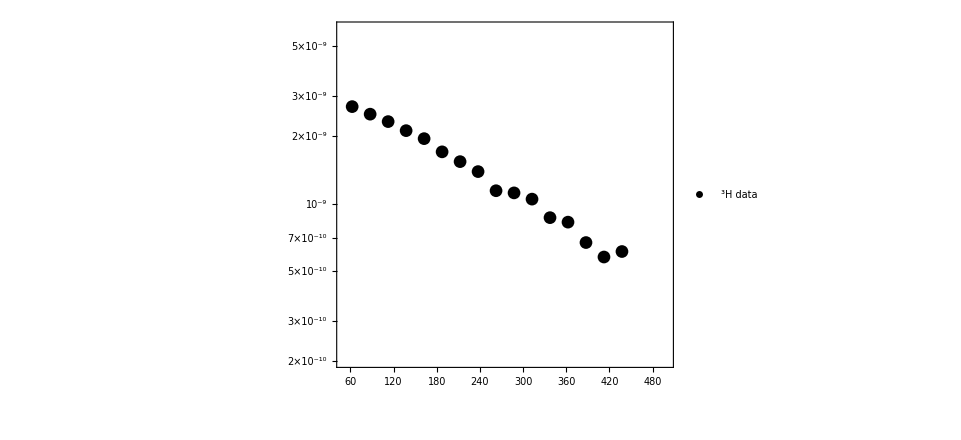

```mathematica
TrytExpMt = ListLogPlot[Trytons,PlotStyle->{Directive[Black,Thick]},PlotRange->{{50,500},{2*10^-10,6*10^-9}},Axes->False,Frame->True,Joined->False,FrameStyle->Directive[Black,Thickness[0.005],14],Epilog->{Rotate[Text[Style["dN/(dy  SubsuperscriptBox[m, ⊥, 2] SubscriptBox[dm, ⊥]) [(MeV/c)^-3]",FontSize->10],{-40,Log[10^(-9)]}],90Degree],Text[Style["m_⊥ - m_(^3) [MeV/c^2]",FontSize->10],{250,Log[10^(-10)]}]},PlotRangeClipping->False,ImagePadding->{{110,20},{50,20}},PlotLegends->Placed[{"^3H data"},{Right,Top}]]
```

```mathematica
TrytMt=Quiet[Table[{Trytons[[i,1]],H3AfrB/(2π)^2 dNB[Trytons[[i,1]]/3+mp,mp,μpB,0]dNB[Trytons[[i,1]]/3+mn,mn,μnB,0]dNB[Trytons[[i,1]]/3+mn,mn,μnB,0]},{i,1,16}]]
```

{{62.5,2.04466×10^-9},{87.5,1.73499×10^-9},{112.5,1.47131×10^-9},{137.5,1.24691×10^-9},{162.5,1.05601×10^-9},{187.5,8.93727×10^-10},{212.5,7.55833×10^-10},{237.5,6.38739×10^-10},{262.5,5.3937×10^-10},{287.5,4.55099×10^-10},{312.5,3.83686×10^-10},{337.5,3.23211×10^-10},{362.5,2.72038×10^-10},{387.5,2.28771×10^-10},{412.5,1.92219×10^-10},{437.5,1.61364×10^-10}}

```mathematica
MtH3 = {{62.5,2.0446600888424555*^-9},{87.5,1.7349902448727635*^-9},{112.5,1.471312118851486*^-9},{137.5,1.2469070513442263*^-9},{162.5,1.056014763472411*^-9},{187.5,8.937270989861061*^-10},{212.5,7.55833477763865*^-10},{237.5,6.387389225241054*^-10},{262.5,5.39370375774212*^-10},{287.5,4.550991240106664*^-10},{312.5,3.836862939017816*^-10},{337.5,3.232111253592717*^-10},{362.5,2.7203822973181744*^-10},{387.5,2.2877099459262067*^-10},{412.5,1.9221856687148756*^-10},{437.5,1.613639589266299*^-10}}
```

{{62.5,2.04466×10^-9},{87.5,1.73499×10^-9},{112.5,1.47131×10^-9},{137.5,1.24691×10^-9},{162.5,1.05601×10^-9},{187.5,8.93727×10^-10},{212.5,7.55833×10^-10},{237.5,6.38739×10^-10},{262.5,5.3937×10^-10},{287.5,4.55099×10^-10},{312.5,3.83686×10^-10},{337.5,3.23211×10^-10},{362.5,2.72038×10^-10},{387.5,2.28771×10^-10},{412.5,1.92219×10^-10},{437.5,1.61364×10^-10}}

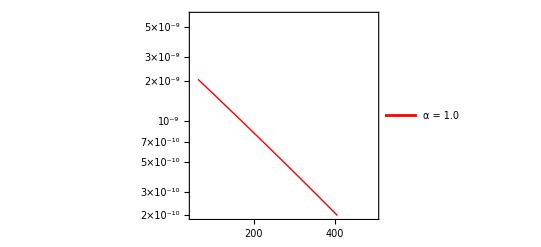

```mathematica
PlotTrytMt = ListLogPlot[MtH3,PlotStyle->{Directive[Red,Thick]},PlotRange->{{50,500},{2*10^-10,6*10^-9}},Axes->False,Frame->True,Joined->True,FrameStyle->Directive[Black,Thickness[0.005],14],Epilog->{Rotate[Text[Style["dN/(dy  SubsuperscriptBox[m, ⊥, 2] SubscriptBox[dm, ⊥]) [(MeV/c)^-3]",FontSize->16],{0,Log[10^(-9)]}],90Degree],Text[Style["m_⊥ - m_(^3) [MeV/c^2]",FontSize->16],{250,Log[1.4*10^(-10)]}]},PlotRangeClipping->False,ImagePadding->{{110,20},{50,20}},PlotLegends->Placed[{"α = 1.0"},{Right,Top}],FrameTicks->{{{{10^(-11),"10^-11"},{2*10^(-11),""},{3*10^(-11),""},{4*10^(-11),""},{5*10^(-11),""},{6*10^(-11),""},{7*10^(-11),""},{8*10^(-11),""},{9*10^(-11),""},{10^(-10),"10^-10"},{2*10^(-10),""},{3*10^(-10),""},{4*10^(-10),""},{5*10^(-10),"5x10^-10"},{6*10^(-10),""},{7*10^(-10),""},{8*10^(-10),""},{9*10^(-10),""},{10^(-9),"10^-9"},{2*10^(-9),""},{3*10^(-9),""},{4*10^(-9),""},{5*10^(-9),"5x10^-9"},{6*10^(-9),""},{7*10^(-9),""},{8*10^(-9),""},{9*10^(-9),""},{10^(-8),"10^-8"}},None},{{0,100,200,300,400,500},None}}]
```

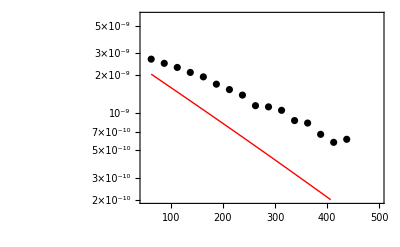

```mathematica
(*Comparison of distributions*)
Show[PlotTrytMt,TrytExpMt]
```

### Transverse mass rescaled

```mathematica
MtH3resc=Table[{MtH3[[i,1]],MtH3[[i,2]]*2.74},{i,1,16}]
```

{{62.5,5.60237×10^-9},{87.5,4.75387×10^-9},{112.5,4.0314×10^-9},{137.5,3.41653×10^-9},{162.5,2.89348×10^-9},{187.5,2.44881×10^-9},{212.5,2.07098×10^-9},{237.5,1.75014×10^-9},{262.5,1.47787×10^-9},{287.5,1.24697×10^-9},{312.5,1.0513×10^-9},{337.5,8.85598×10^-10},{362.5,7.45385×10^-10},{387.5,6.26833×10^-10},{412.5,5.26679×10^-10},{437.5,4.42137×10^-10}}

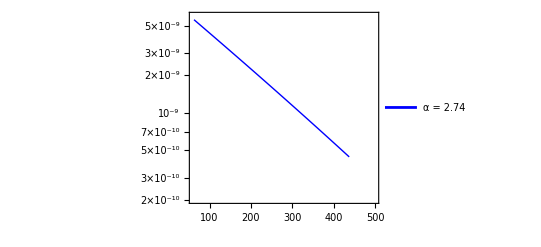

```mathematica
PlotTrytMtResc = ListLogPlot[MtH3resc,PlotStyle->{Directive[Blue,Thick]},PlotRange->{{60,500},{2*10^-10,6*10^-9}},Axes->False,Frame->True,Joined->True,FrameStyle->Directive[Black,Thickness[0.005],14],Epilog->{Rotate[Text[Style["dN/(dy  SubsuperscriptBox[m, ⊥, 2] SubscriptBox[dm, ⊥]) [(MeV/c)^-3]",FontSize->10],{-90,Log[10^(-9)]}],90Degree],Text[Style["m_⊥ - m_(^3) [MeV/c^2]",FontSize->10],{250,Log[10^(-10)]}]},PlotRangeClipping->False,ImagePadding->{{110,20},{50,20}},PlotLegends->Placed[{"α = 2.74"},{Right,Top}]]
```

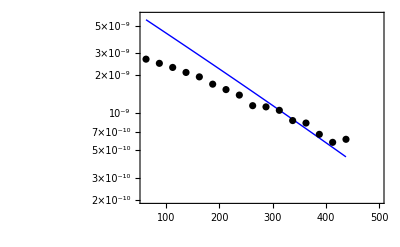

```mathematica
Show[PlotTrytMtResc,TrytExpMt]
(*****************************************************************************************************)
```

### Rapidity distribution

```mathematica
(*Tritium rapidity distribution in case B*)
```

```mathematica
RapidityDistributionB=Quiet[Table[{TrytonsY[[i,1]],NIntegrate[(mt+mp+2mn)^2 Cosh[TrytonsY[[i,1]]] AfrB/(2π )^2 dNB[mt/3+mp,mp,μpB,TrytonsY[[i,1]]]dNB[mt/3+mn,mn,μnB,TrytonsY[[i,1]]]dNB[mt/3+mn,mn,μnB,TrytonsY[[i,1]]],{mt,0,1000}]},{i,1,13}]]
```

{{-0.6,0.591403},{-0.5,1.11449},{-0.4,1.81894},{-0.3,2.61341},{-0.2,3.35096},{-0.1,3.87379},{0.,4.06278},{0.1,3.87379},{0.2,3.35096},{0.3,2.61341},{0.4,1.81894},{0.5,1.11449},{0.6,0.591403}}

```mathematica
rapH3={{-0.6,0.5914029185950526},{-0.5,1.1144907269441533},{-0.4,1.8189363953128461},{-0.3,2.6134062602696737},{-0.2,3.350955551566881},{-0.1,3.8737942516153483},{0.,4.062778629874862},{0.1,3.87379215198085},{0.2,3.3509570662992227},{0.3,2.6134062655513497},{0.4,1.8189357400547295},{0.5,1.1144904824910076},{0.6,0.5914032061471987}}
```

{{-0.6,0.591403},{-0.5,1.11449},{-0.4,1.81894},{-0.3,2.61341},{-0.2,3.35096},{-0.1,3.87379},{0.,4.06278},{0.1,3.87379},{0.2,3.35096},{0.3,2.61341},{0.4,1.81894},{0.5,1.11449},{0.6,0.591403}}

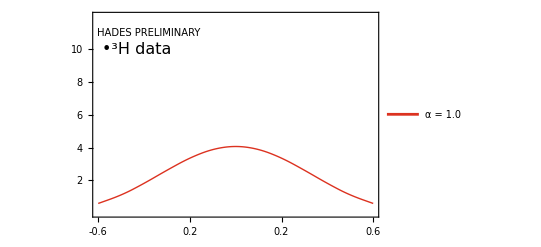

```mathematica
PlotRapidityDistributionB =ListPlot[rapH3,PlotStyle->{Directive[RGBColor["#DC3220"],Thick]},PlotRange->{{-0.6,0.6},{0,12}},Axes->False,Frame->True,Joined->True,FrameStyle->Directive[Black,Thickness[0.005],14],Epilog->{Rotate[Text[Style["dN / dy",FontSize->15],{-0.76,6}],90Degree],Text[Style["y",FontSize->16],{0,-1.4}],Text[Style["•^3H data",FontSize->16],{-0.43,10}],Text[Style["  HADES PRELIMINARY",FontSize->10],{-0.38,11}]},PlotRangeClipping->False,ImagePadding->{{50,0},{50,0}},PlotLegends->Placed[LineLegend[{"α = 1.0"},LegendMarkerSize->{30,16}],{Right,Top}],InterpolationOrder->2,FrameTicks->{{{{0.5,""},{1,""},{1.5,""},{2,"2",.02},{2.5,""},{3,""},{3.5,""},{4,"4",.02},{4.5,""},{5,""},{5.5,""},{6,"6",.02},{6.5,""},{7,""},{7.5,""},{8,"8",.02},{8.5,""},{9,""},{9.5,""},{10,"10",.02},{10.5,""},{11,""},{11.5,""}},{{0.5,""},{1,""},{1.5,""},{2,"2",.02},{2.5,""},{3,""},{3.5,""},{4,"4",.02},{4.5,""},{5,""},{5.5,""},{6,"6",.02},{6.5,""},{7,""},{7.5,""},{8,"8",.02},{8.5,""},{9,""},{9.5,""},{10,"10",.02},{10.5,""},{11,""},{11.5,""}}},{{{-0.6,"-0.6",.02},{-0.55,""},{-0.5,""},{-0.45,""},{-0.4,"-0.4",.02},{-0.35,""},{-0.3,""},{-0.25,""},{-0.2,"0.2",.02},{-0.15,""},{-0.1,""},{-0.05,""},{0,"0",.02},{0.05,""},{0.1,""},{0.15,""},{0.2,"0.2",.02},{0.25,""},{0.3,""},{0.35,""},{0.4,"0.4",.02},{0.45,""},{0.5,""},{0.55,""},{0.6,"0.6",.02}},{{-0.6,"-0.6",.02},{-0.55,""},{-0.5,""},{-0.45,""},{-0.4,"-0.4",.02},{-0.35,""},{-0.3,""},{-0.25,""},{-0.2,"0.2",.02},{-0.15,""},{-0.1,""},{-0.05,""},{0,"0",.02},{0.05,""},{0.1,""},{0.15,""},{0.2,"0.2",.02},{0.25,""},{0.3,""},{0.35,""},{0.4,"0.4",.02},{0.45,""},{0.5,""},{0.55,""},{0.6,"0.6",.02}}}}]
```

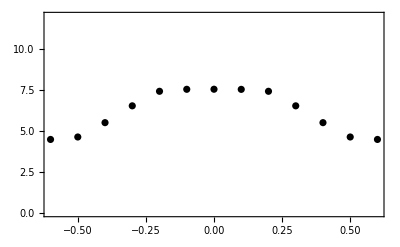

```mathematica
TrytExp = ListPlot[TrytonsY,PlotStyle->{Directive[Black,Thick]},PlotRange->{{-0.6,0.6},{0,12}},Axes->False,Frame->True,Joined->False,FrameStyle->Directive[Black,Thickness[0.005],14],Epilog->{Rotate[Text[Style["dN/dy",FontSize->12],{-0.7,5}],90Degree],Text[Style["y",FontSize->14],{0,-1.5}]},PlotRangeClipping->False,ImagePadding->{{50,10},{50,10}}]
```

```mathematica
(*Comparison of rapidity distributions*)
```

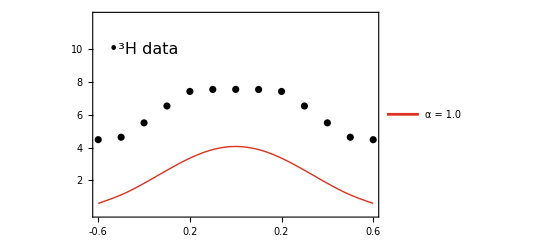

```mathematica
Show[{PlotRapidityDistributionB,TrytExp}]
```

### Rapidity rescaled

```mathematica
rapH3resc = Table[{rapH3[[i,1]],rapH3[[i,2]]*2.74},{i,1,13}]
```

{{-0.6,1.62044},{-0.5,3.0537},{-0.4,4.98389},{-0.3,7.16073},{-0.2,9.18162},{-0.1,10.6142},{0.,11.132},{0.1,10.6142},{0.2,9.18162},{0.3,7.16073},{0.4,4.98388},{0.5,3.0537},{0.6,1.62044}}

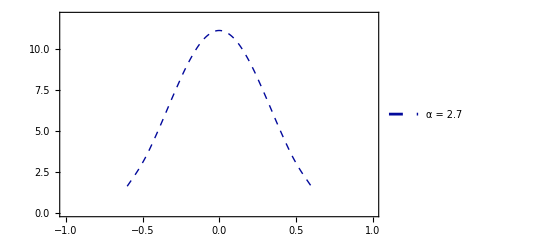

```mathematica
PlotrapH3resc =ListPlot[rapH3resc,PlotStyle->{Directive[RGBColor["#030A9C"],Dashed,Thick]},PlotRange->{{-1,1},{0,12}},Axes->False,Frame->True,Joined->True,FrameStyle->Directive[Black,Thickness[0.005],14],Epilog->{Rotate[Text[Style["dN/dy",FontSize->12],{-1.2,5}],90Degree],Text[Style["y",FontSize->14],{0,-1.5}]},PlotRangeClipping->False,ImagePadding->{{50,10},{50,10}},PlotLegends->Placed[LineLegend[{"α = 2.7"},LegendMarkerSize->{30,16}],{Right,Top}],InterpolationOrder->2]
```

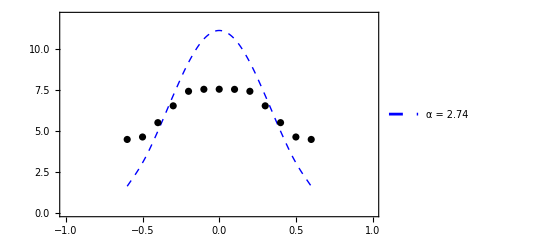

```mathematica
Show[{PlotrapH3resc,ListPlot[TrytonsY,PlotStyle->Black,AxesLabel->{"m_t-m_0 [MeV]","1/((m^2)_t)dN/dm_t|_(y = 0) [MeV^-3]"},PlotLabel->"Tritium distribution",PlotStyle->Thick,PlotStyle->Black]}]
```

## He3

### Transverse mass spectrum

```mathematica
(*Transverse mass He3 distribution in case B*)
```

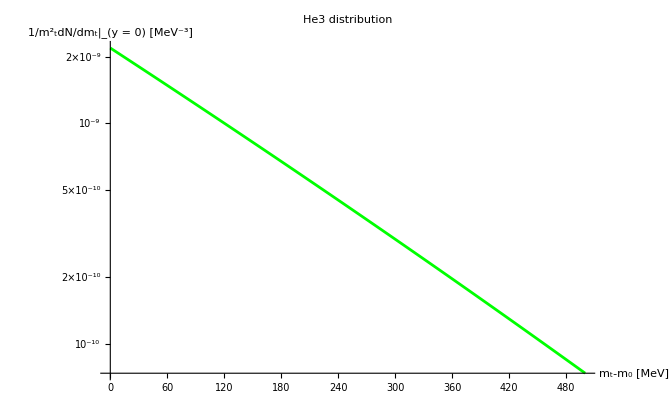

```mathematica
He3DistributionB=LogPlot[{He3AfrB/(2π)^2 dNB[mt/3+mp,mp,μpB,0]dNB[mt/3+mp,mp,μpB,0]dNB[mt/3+mn,mn,μnB,0]},{mt,0,500},PlotStyle->Green,AxesLabel->{"m_t-m_0 [MeV]","1/((m^2)_t)dN/dm_t|_(y = 0) [MeV^-3]",Thick},PlotLabel->"He3 distribution",AxesStyle->Thick]
```

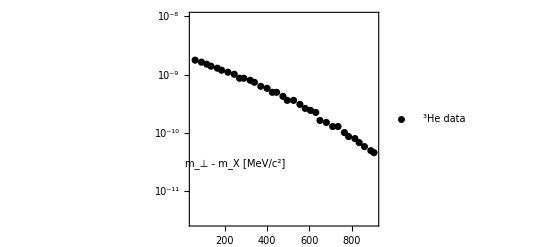

```mathematica
He3ExpMt = ListLogPlot[He3,PlotStyle->{Directive[Black,Thick]},PlotRange->{{50,910},{3*10^-12,10^-8}},Axes->False,Frame->True,Joined->False,FrameStyle->Directive[Black,Thickness[0.005],14],Epilog->{Rotate[Text[Style["dN/(dy  SubsuperscriptBox[m, ⊥, 2] SubscriptBox[dm, ⊥]) [(MeV/c)^-3]",FontSize->10],{-180,Log[10^(-9)]}],90Degree],Text[Style["m_⊥ - m_X [MeV/c^2]",FontSize->10],{250,Log[3*10^(-11)]}]},PlotRangeClipping->False,ImagePadding->{{110,20},{50,20}},PlotLegends->Placed[{"^3He data"},{Right,Top}]]
```

```mathematica
He3Mt=Quiet[Table[{He3[[i,1]],He3AfrB/(2π)^2 dNB[He3[[i,1]]/3+mp,mp,μpB,0]dNB[He3[[i,1]]/3+mp,mp,μpB,0]dNB[He3[[i,1]]/3+mn,mn,μnB,0]},{i,1,34}]]
```

{{60,1.48524×10^-9},{90,1.21986×10^-9},{115,1.03445×10^-9},{135,9.0613×10^-10},{165,7.42168×10^-10},{185,6.49284×10^-10},{215,5.30775×10^-10},{245,4.33381×10^-10},{270,3.6568×10^-10},{290,3.1902×10^-10},{320,2.59682×10^-10},{340,2.26232×10^-10},{370,1.83763×10^-10},{400,1.49075×10^-10},{425,1.251×10^-10},{445,1.08656×10^-10},{475,8.78569×10^-11},{495,7.6197×10^-11},{525,6.14752×10^-11},{555,4.95321×10^-11},{580,4.13304×10^-11},{605,3.44551×10^-11},{630,2.86973×10^-11},{650,2.47756×10^-11},{680,1.98531×10^-11},{710,1.58881×10^-11},{735,1.31829×10^-11},{765,1.05254×10^-11},{785,9.05217×10^-12},{815,7.21229×10^-12},{835,6.1943×10^-12},{860,5.11756×10^-12},{890,4.0651×10^-12},{905,3.62146×10^-12}}

```mathematica
MtHe3={{60,1.4852438471737949*^-9},{90,1.2198639769877324*^-9},{115,1.0344537344703923*^-9},{135,9.061299508174777*^-10},{165,7.421682031809184*^-10},{185,6.492837862104796*^-10},{215,5.307748845120324*^-10},{245,4.3338079211519*^-10},{270,3.6567954674668416*^-10},{290,3.190203421567211*^-10},{320,2.596824649849465*^-10},{340,2.2623206821740753*^-10},{370,1.83763261751957*^-10},{400,1.4907467700780157*^-10},{425,1.2509986117415414*^-10},{445,1.0865626522783665*^-10},{475,8.785687997455279*^-11},{495,7.619696553131263*^-11},{525,6.147523286150776*^-11},{555,4.953211755037416*^-11},{580,4.133039665012014*^-11},{605,3.445510626682322*^-11},{630,2.8697290050191043*^-11},{650,2.4775640660133473*^-11},{680,1.9853107326671878*^-11},{710,1.588812168689939*^-11},{735,1.3182918886264052*^-11},{765,1.0525371777007124*^-11},{785,9.052165336947533*^-12},{815,7.212294019225772*^-12},{835,6.194296407128202*^-12},{860,5.117564898030293*^-12},{890,4.065103503991328*^-12},{905,3.62146337773399*^-12}}
```

{{60,1.48524×10^-9},{90,1.21986×10^-9},{115,1.03445×10^-9},{135,9.0613×10^-10},{165,7.42168×10^-10},{185,6.49284×10^-10},{215,5.30775×10^-10},{245,4.33381×10^-10},{270,3.6568×10^-10},{290,3.1902×10^-10},{320,2.59682×10^-10},{340,2.26232×10^-10},{370,1.83763×10^-10},{400,1.49075×10^-10},{425,1.251×10^-10},{445,1.08656×10^-10},{475,8.78569×10^-11},{495,7.6197×10^-11},{525,6.14752×10^-11},{555,4.95321×10^-11},{580,4.13304×10^-11},{605,3.44551×10^-11},{630,2.86973×10^-11},{650,2.47756×10^-11},{680,1.98531×10^-11},{710,1.58881×10^-11},{735,1.31829×10^-11},{765,1.05254×10^-11},{785,9.05217×10^-12},{815,7.21229×10^-12},{835,6.1943×10^-12},{860,5.11756×10^-12},{890,4.0651×10^-12},{905,3.62146×10^-12}}

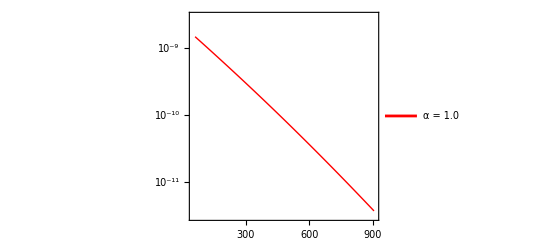

```mathematica
PlotHe3Mt = ListLogPlot[MtHe3,PlotStyle->{Directive[Red,Thick]},PlotRange->{{50,910},{3*10^-12,3*10^-9}},Axes->False,Frame->True,Joined->True,FrameStyle->Directive[Black,Thickness[0.005],14],Epilog->{Rotate[Text[Style["dN/(dy  SubsuperscriptBox[m, ⊥, 2] SubscriptBox[dm, ⊥]) [(MeV/c)^-3]",FontSize->16],{-100,Log[10^(-10)]}],90Degree],Text[Style["m_⊥ - m_(SuperscriptBox[, 3]He) [MeV/c^2]",FontSize->16],{450,Log[1.5*10^(-12)]}]},PlotRangeClipping->False,ImagePadding->{{110,20},{50,20}},PlotLegends->Placed[{"α = 1.0"},{Right,Top}],FrameTicks->{{{{10^(-11),"10^-11"},{2*10^(-11),""},{3*10^(-11),""},{4*10^(-11),""},{5*10^(-11),""},{6*10^(-11),""},{7*10^(-11),""},{8*10^(-11),""},{9*10^(-11),""},{10^(-10),"10^-10"},{2*10^(-10),""},{3*10^(-10),""},{4*10^(-10),""},{5*10^(-10),""},{6*10^(-10),""},{7*10^(-10),""},{8*10^(-10),""},{9*10^(-10),""},{10^(-9),"10^-9"},{2*10^(-9),""},{3*10^(-9),""},{4*10^(-9),""},{5*10^(-9),""},{6*10^(-9),""},{7*10^(-9),""},{8*10^(-9),""},{9*10^(-9),""},{10^(-8),"10^-8"}},None},{{0,100,200,300,400,500,600,700,800,900,1000},None}}]
```

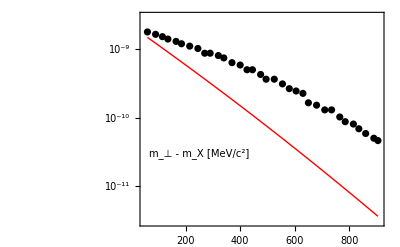

```mathematica
(*Comparison of distributions*)
Show[PlotHe3Mt,He3ExpMt]
```

### Transverse mass rescaled

```mathematica
MtHe3resc=Table[{MtHe3[[i,1]],MtHe3[[i,2]]*2.01},{i,1,34}]
```

{{60,2.98534×10^-9},{90,2.45193×10^-9},{115,2.07925×10^-9},{135,1.82132×10^-9},{165,1.49176×10^-9},{185,1.30506×10^-9},{215,1.06686×10^-9},{245,8.71095×10^-10},{270,7.35016×10^-10},{290,6.41231×10^-10},{320,5.21962×10^-10},{340,4.54726×10^-10},{370,3.69364×10^-10},{400,2.9964×10^-10},{425,2.51451×10^-10},{445,2.18399×10^-10},{475,1.76592×10^-10},{495,1.53156×10^-10},{525,1.23565×10^-10},{555,9.95596×10^-11},{580,8.30741×10^-11},{605,6.92548×10^-11},{630,5.76816×10^-11},{650,4.9799×10^-11},{680,3.99047×10^-11},{710,3.19351×10^-11},{735,2.64977×10^-11},{765,2.1156×10^-11},{785,1.81949×10^-11},{815,1.44967×10^-11},{835,1.24505×10^-11},{860,1.02863×10^-11},{890,8.17086×10^-12},{905,7.27914×10^-12}}

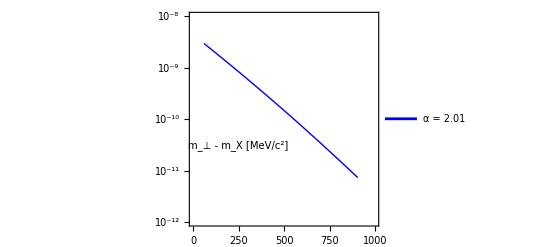

```mathematica
PlotHe3MtResc = ListLogPlot[MtHe3resc,PlotStyle->{Directive[Blue,Thick]},PlotRange->{{0,1000},{10^-12,10^-8}},Axes->False,Frame->True,Joined->True,FrameStyle->Directive[Black,Thickness[0.005],14],Epilog->{Rotate[Text[Style["dN/(dy  SubsuperscriptBox[m, ⊥, 2] SubscriptBox[dm, ⊥]) [(MeV/c)^-3]",FontSize->10],{-180,Log[10^(-9)]}],90Degree],Text[Style["m_⊥ - m_X [MeV/c^2]",FontSize->10],{250,Log[3*10^(-11)]}]},PlotRangeClipping->False,ImagePadding->{{110,20},{50,20}},PlotLegends->Placed[{"α = 2.01"},{Right,Top}]]
```

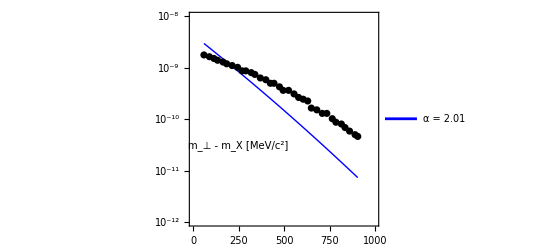

```mathematica
Show[PlotHe3MtResc,He3ExpMt]
(*****************************************************************************************************)
```

### Rapidity distribution

```mathematica
(*He3 rapidity distribution in case B*)
```

```mathematica
He3RapidityDistributionB=Quiet[Table[{TrytonsY[[i,1]],NIntegrate[(mt+2mp+mn)^2 Cosh[TrytonsY[[i,1]]] He3AfrB/(2π)^2 dNB[mt/3+mp,mp,μpB,TrytonsY[[i,1]]]dNB[mt/3+mp,mp,μpB,TrytonsY[[i,1]]]dNB[mt/3+mn,mn,μnB,TrytonsY[[i,1]]],{mt,0,1000}]},{i,1,13}]]
```

{{-0.6,0.421296},{-0.5,0.794537},{-0.4,1.29707},{-0.3,1.86361},{-0.2,2.38941},{-0.1,2.76207},{0.,2.89676},{0.1,2.76207},{0.2,2.38941},{0.3,1.86361},{0.4,1.29707},{0.5,0.794537},{0.6,0.421296}}

```mathematica
rapHe3 ={{-0.6,0.421295806902789},{-0.5,0.7945366033948419},{-0.4,1.297070103248663},{-0.3,1.8636132387775888},{-0.2,2.3894083039913587},{-0.1,2.762070092750687},{0.,2.896761687919559},{0.1,2.7620694268825945},{0.2,2.3894088117849166},{0.3,1.863613200481666},{0.4,1.297068656097244},{0.5,0.794536628704457},{0.6,0.42129561861289505}}
```

{{-0.6,0.421296},{-0.5,0.794537},{-0.4,1.29707},{-0.3,1.86361},{-0.2,2.38941},{-0.1,2.76207},{0.,2.89676},{0.1,2.76207},{0.2,2.38941},{0.3,1.86361},{0.4,1.29707},{0.5,0.794537},{0.6,0.421296}}

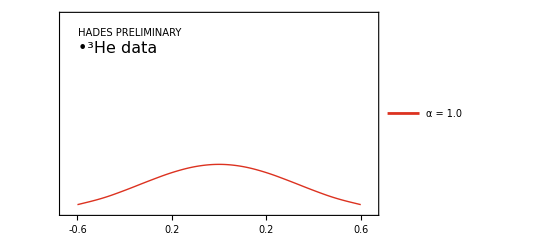

```mathematica
He3PlotRapidityDistributionB =ListPlot[rapHe3,PlotStyle->{Directive[RGBColor["#DC3220"],Thick]},PlotRange->{{-0.65,0.65},{0,12}},Axes->False,Frame->True,Joined->True,FrameStyle->Directive[Black,Thickness[0.005],14],Epilog->{Text[Style["y",FontSize->16],{0,-1.5}],Text[Style["•^3He data",FontSize->16],{-0.43,10}],Text[Style["  HADES PRELIMINARY",FontSize->10],{-0.38,11}]},PlotRangeClipping->False,ImagePadding->{{50,0},{50,0}},PlotLegends->Placed[LineLegend[{"α = 1.0"},LegendMarkerSize->{30,16}],{Right,Top}],InterpolationOrder->2,FrameTicks->{{{{0.5,""},{1,""},{1.5,""},{2,"",.02},{2.5,""},{3,""},{3.5,""},{4,"",.02},{4.5,""},{5,""},{5.5,""},{6,"",.02},{6.5,""},{7,""},{7.5,""},{8,"",.02},{8.5,""},{9,""},{9.5,""},{10,"",.02},{10.5,""},{11,""},{11.5,""}},{{0.5,""},{1,""},{1.5,""},{2,"",.02},{2.5,""},{3,""},{3.5,""},{4,"",.02},{4.5,""},{5,""},{5.5,""},{6,"",.02},{6.5,""},{7,""},{7.5,""},{8,"",.02},{8.5,""},{9,""},{9.5,""},{10,"",.02},{10.5,""},{11,""},{11.5,""}}},{{{-0.6,"-0.6",.02},{-0.55,""},{-0.5,""},{-0.45,""},{-0.4,"-0.4",.02},{-0.35,""},{-0.3,""},{-0.25,""},{-0.2,"0.2",.02},{-0.15,""},{-0.1,""},{-0.05,""},{0,"0",.02},{0.05,""},{0.1,""},{0.15,""},{0.2,"0.2",.02},{0.25,""},{0.3,""},{0.35,""},{0.4,"0.4",.02},{0.45,""},{0.5,""},{0.55,""},{0.6,"0.6",.02}},{{-0.6,"-0.6",.02},{-0.55,""},{-0.5,""},{-0.45,""},{-0.4,"-0.4",.02},{-0.35,""},{-0.3,""},{-0.25,""},{-0.2,"0.2",.02},{-0.15,""},{-0.1,""},{-0.05,""},{0,"0",.02},{0.05,""},{0.1,""},{0.15,""},{0.2,"0.2",.02},{0.25,""},{0.3,""},{0.35,""},{0.4,"0.4",.02},{0.45,""},{0.5,""},{0.55,""},{0.6,"0.6",.02}}}}]
```

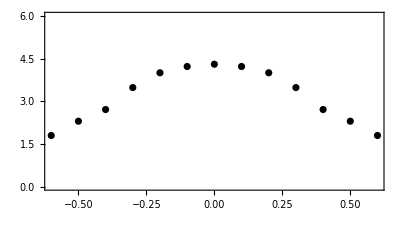

```mathematica
He3Exp = ListPlot[He3Y,PlotStyle->{Directive[Black,Thick]},PlotRange->{{-0.6,0.6},{0,6}},Axes->False,Frame->True,Joined->False,FrameStyle->Directive[Black,Thickness[0.005],14],Epilog->{Rotate[Text[Style["dN/dy",FontSize->16],{-0.7,5}],90Degree],Text[Style["y",FontSize->16],{0,-1.5}]},PlotRangeClipping->False,ImagePadding->{{50,10},{50,10}}]
```

```mathematica
(*Comparison of rapidity distributions*)
```

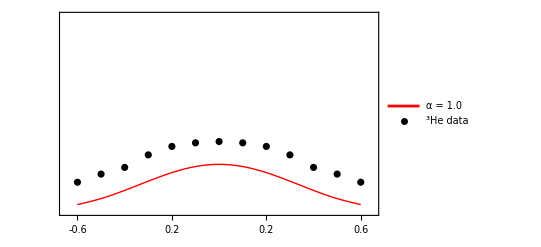

```mathematica
Show[{He3PlotRapidityDistributionB,He3Exp}]
```

### Rapidity rescaled

```mathematica
rapHe3resc = Table[{rapHe3[[i,1]],rapHe3[[i,2]]*2.01},{i,1,13}]
```

```mathematica
{{-0.6,0.8468045718746058},{-0.5,1.5970185728236321},{-0.4,2.6071109075298122},{-0.3,3.745862609942953},{-0.2,4.8027106910226305},{-0.1,5.55176088642888},{0.,5.822490992718312},{0.1,5.551759548034014},{0.2,4.802711711687682},{0.3,3.745862532968148},{0.4,2.60710799875546},{0.5,1.5970186236959583},{0.6,0.8468041934119189}}
```

{{-0.6,0.846805},{-0.5,1.59702},{-0.4,2.60711},{-0.3,3.74586},{-0.2,4.80271},{-0.1,5.55176},{0.,5.82249},{0.1,5.55176},{0.2,4.80271},{0.3,3.74586},{0.4,2.60711},{0.5,1.59702},{0.6,0.846804}}

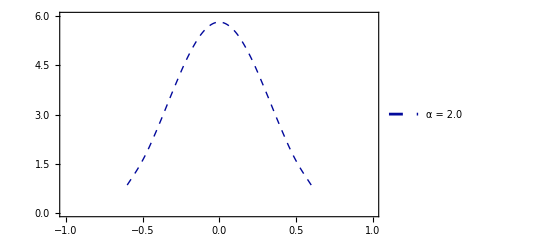

```mathematica
PlotrapHe3resc =ListPlot[rapHe3resc,PlotStyle->{Directive[RGBColor["#030A9C"],Dashed,Thick]},PlotRange->{{-1,1},{0,6}},Axes->False,Frame->True,Joined->True,FrameStyle->Directive[Black,Thickness[0.005],14],Epilog->{Rotate[Text[Style["dN/dy",FontSize->12],{-1.2,3}],90Degree],Text[Style["y",FontSize->14],{0,-0.75}]},PlotRangeClipping->False,ImagePadding->{{50,10},{50,10}},PlotLegends->Placed[LineLegend[{"α = 2.0"},LegendMarkerSize->{30,16}],{Right,Top}],InterpolationOrder->2]
```

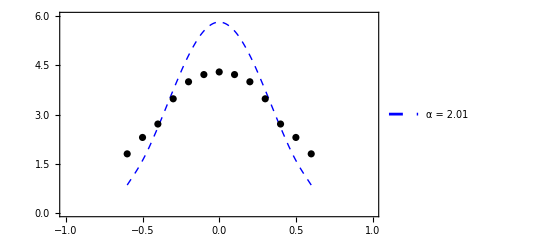

```mathematica
Show[{PlotrapHe3resc ,ListPlot[He3Y,PlotStyle->Black,AxesLabel->{"m_t-m_0 [MeV]","1/((m^2)_t)dN/dm_t|_(y = 0) [MeV^-3]"},PlotLabel->"Tritium distribution",PlotStyle->Thick,PlotStyle->Black]}]
```

## Fitting

### Model spectra

```mathematica
mtH3 = {{62.5,2.0446600888424555*^-9},{87.5,1.7349902448727635*^-9},{112.5,1.471312118851486*^-9},{137.5,1.2469070513442263*^-9},{162.5,1.056014763472411*^-9},{187.5,8.937270989861061*^-10},{212.5,7.55833477763865*^-10},{237.5,6.387389225241054*^-10},{262.5,5.39370375774212*^-10},{287.5,4.550991240106664*^-10},{312.5,3.836862939017816*^-10},{337.5,3.232111253592717*^-10},{362.5,2.7203822973181744*^-10},{387.5,2.2877099459262067*^-10},{412.5,1.9221856687148756*^-10},{437.5,1.613639589266299*^-10}}
```

{{62.5,2.04466×10^-9},{87.5,1.73499×10^-9},{112.5,1.47131×10^-9},{137.5,1.24691×10^-9},{162.5,1.05601×10^-9},{187.5,8.93727×10^-10},{212.5,7.55833×10^-10},{237.5,6.38739×10^-10},{262.5,5.3937×10^-10},{287.5,4.55099×10^-10},{312.5,3.83686×10^-10},{337.5,3.23211×10^-10},{362.5,2.72038×10^-10},{387.5,2.28771×10^-10},{412.5,1.92219×10^-10},{437.5,1.61364×10^-10}}

```mathematica
MtHe3={{60,1.4852438471737949*^-9},{90,1.2198639769877324*^-9},{115,1.0344537344703923*^-9},{135,9.061299508174777*^-10},{165,7.421682031809184*^-10},{185,6.492837862104796*^-10},{215,5.307748845120324*^-10},{245,4.3338079211519*^-10},{270,3.6567954674668416*^-10},{290,3.190203421567211*^-10},{320,2.596824649849465*^-10},{340,2.2623206821740753*^-10},{370,1.83763261751957*^-10},{400,1.4907467700780157*^-10},{425,1.2509986117415414*^-10},{445,1.0865626522783665*^-10},{475,8.785687997455279*^-11},{495,7.619696553131263*^-11},{525,6.147523286150776*^-11},{555,4.953211755037416*^-11},{580,4.133039665012014*^-11},{605,3.445510626682322*^-11},{630,2.8697290050191043*^-11},{650,2.4775640660133473*^-11},{680,1.9853107326671878*^-11},{710,1.588812168689939*^-11},{735,1.3182918886264052*^-11},{765,1.0525371777007124*^-11},{785,9.052165336947533*^-12},{815,7.212294019225772*^-12},{835,6.194296407128202*^-12},{860,5.117564898030293*^-12},{890,4.065103503991328*^-12},{905,3.62146337773399*^-12}}
```

{{60,1.48524×10^-9},{90,1.21986×10^-9},{115,1.03445×10^-9},{135,9.0613×10^-10},{165,7.42168×10^-10},{185,6.49284×10^-10},{215,5.30775×10^-10},{245,4.33381×10^-10},{270,3.6568×10^-10},{290,3.1902×10^-10},{320,2.59682×10^-10},{340,2.26232×10^-10},{370,1.83763×10^-10},{400,1.49075×10^-10},{425,1.251×10^-10},{445,1.08656×10^-10},{475,8.78569×10^-11},{495,7.6197×10^-11},{525,6.14752×10^-11},{555,4.95321×10^-11},{580,4.13304×10^-11},{605,3.44551×10^-11},{630,2.86973×10^-11},{650,2.47756×10^-11},{680,1.98531×10^-11},{710,1.58881×10^-11},{735,1.31829×10^-11},{765,1.05254×10^-11},{785,9.05217×10^-12},{815,7.21229×10^-12},{835,6.1943×10^-12},{860,5.11756×10^-12},{890,4.0651×10^-12},{905,3.62146×10^-12}}

```mathematica
rapH3={{-0.6,0.5914029185950526},{-0.5,1.1144907269441533},{-0.4,1.8189363953128461},{-0.3,2.6134062602696737},{-0.2,3.350955551566881},{-0.1,3.8737942516153483},{0.,4.062778629874862},{0.1,3.87379215198085},{0.2,3.3509570662992227},{0.3,2.6134062655513497},{0.4,1.8189357400547295},{0.5,1.1144904824910076},{0.6,0.5914032061471987}}
```

{{-0.6,0.591403},{-0.5,1.11449},{-0.4,1.81894},{-0.3,2.61341},{-0.2,3.35096},{-0.1,3.87379},{0.,4.06278},{0.1,3.87379},{0.2,3.35096},{0.3,2.61341},{0.4,1.81894},{0.5,1.11449},{0.6,0.591403}}

```mathematica
rapHe3 = {{-0.6,0.421295806902789},{-0.5,0.7945366033948419},{-0.4,1.297070103248663},{-0.3,1.8636132387775888},{-0.2,2.3894083039913587},{-0.1,2.762070092750687},{0.,2.896761687919559},{0.1,2.7620694268825945},{0.2,2.3894088117849166},{0.3,1.863613200481666},{0.4,1.297068656097244},{0.5,0.794536628704457},{0.6,0.42129561861289505}}
```

{{-0.6,0.421296},{-0.5,0.794537},{-0.4,1.29707},{-0.3,1.86361},{-0.2,2.38941},{-0.1,2.76207},{0.,2.89676},{0.1,2.76207},{0.2,2.38941},{0.3,1.86361},{0.4,1.29707},{0.5,0.794537},{0.6,0.421296}}

### Minimalization of α multiplier

```mathematica
fH3[α_]:=1/13 Sum[(α rapH3[[i,2]]-TrytonsY[[i,2]])^2/TrytonsY[[i,2]]^2,{i,1,13}]
fHe3[α_]:=1/13 Sum[(α rapHe3[[i,2]]-He3Y[[i,2]])^2/He3Y[[i,2]]^2,{i,1,13}]
```

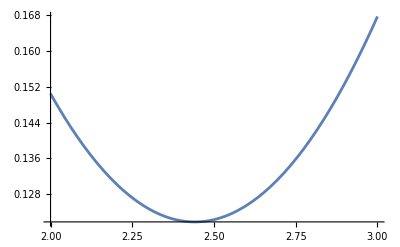

```mathematica
Plot[fH3[α],{α,2,3}]
```

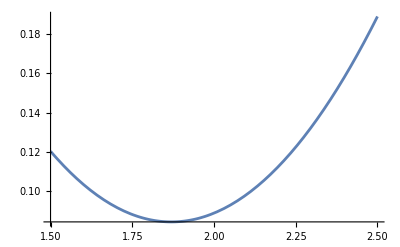

```mathematica
Plot[fHe3[α],{α,1.5,2.5}]
```

```mathematica
NSolve[fH3'[x]==0,x]
```

{{x→2.44133}}

```mathematica
NSolve[fHe3'[x]==0,x]
```

{{x→1.86965}}

```mathematica
fH3[2.4413263822101334]
```

0.121778

```mathematica
√fH3[2.4413263822101334]
```

0.348967

```mathematica
fHe3[1.8696526632986925]
```

0.0845944

```mathematica
√fHe3[1.8696526632986925]
```

0.290851

### Optimalization for tritium

#### Transverse mass

```mathematica
MtH3opt=Table[{TrytMt[[i,1]],TrytMt[[i,2]]*2.44},{i,1,16}]
```

{{62.5,4.98897×10^-9},{87.5,4.23338×10^-9},{112.5,3.59×10^-9},{137.5,3.04245×10^-9},{162.5,2.57668×10^-9},{187.5,2.18069×10^-9},{212.5,1.84423×10^-9},{237.5,1.55852×10^-9},{262.5,1.31606×10^-9},{287.5,1.11044×10^-9},{312.5,9.36195×10^-10},{337.5,7.88635×10^-10},{362.5,6.63773×10^-10},{387.5,5.58201×10^-10},{412.5,4.69013×10^-10},{437.5,3.93728×10^-10}}

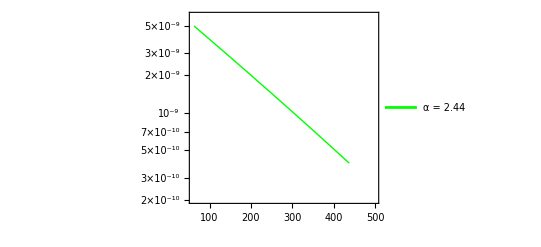

```mathematica
PlotTrytMtOpt = ListLogPlot[MtH3opt,PlotStyle->{Directive[Green,Thick]},PlotRange->{{60,500},{2*10^-10,6*10^-9}},Axes->False,Frame->True,Joined->True,FrameStyle->Directive[Black,Thickness[0.005],14],Epilog->{Rotate[Text[Style["dN/(dy  SubsuperscriptBox[m, ⊥, 2] SubscriptBox[dm, ⊥]) [(MeV/c)^-3]",FontSize->10],{-90,Log[10^(-9)]}],90Degree],Text[Style["m_⊥ - m_(^3) [MeV/c^2]",FontSize->10],{250,Log[10^(-10)]}]},PlotRangeClipping->False,ImagePadding->{{110,20},{50,20}},PlotLegends->Placed[{"α = 2.44"},{Right,Top}]]
```

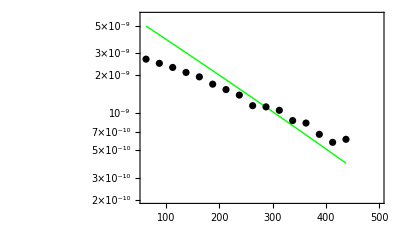

```mathematica
Show[PlotTrytMtOpt,TrytExpMt]
```

#### Rapidity

```mathematica
rapH3opt= Table[{rapH3[[i,1]],rapH3[[i,2]]*2.44},{i,1,13}]
```

{{-0.6,1.44302},{-0.5,2.71936},{-0.4,4.4382},{-0.3,6.37671},{-0.2,8.17633},{-0.1,9.45206},{0.,9.91318},{0.1,9.45205},{0.2,8.17634},{0.3,6.37671},{0.4,4.4382},{0.5,2.71936},{0.6,1.44302}}

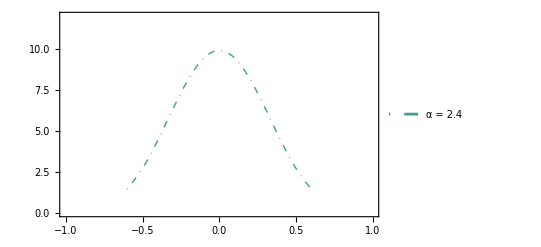

```mathematica
PlotrapH3opt=ListPlot[rapH3opt,PlotStyle->{Directive[RGBColor["#479C8E"],DotDashed,Thick]},PlotRange->{{-1,1},{0,12}},Axes->False,Frame->True,Joined->True,FrameStyle->Directive[Black,Thickness[0.005],14],Epilog->{Rotate[Text[Style["dN/dy",FontSize->12],{-1.2,5}],90Degree],Text[Style["y",FontSize->14],{0,-1.5}]},PlotRangeClipping->False,ImagePadding->{{50,10},{50,10}},PlotLegends->Placed[LineLegend[{"α = 2.4"},LegendMarkerSize->{30,16}],{Right,Top}],InterpolationOrder->2]
```

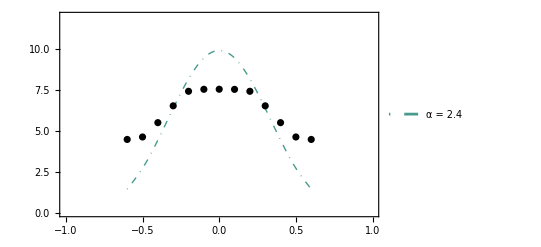

```mathematica
Show[{PlotrapH3opt,TrytExp}]
```

### Optimalization for He3

#### Transverse mass

```mathematica
MtHe3opt=Table[{MtHe3[[i,1]],MtHe3[[i,2]]*1.87},{i,1,34}]
```

{{60,2.77741×10^-9},{90,2.28115×10^-9},{115,1.93443×10^-9},{135,1.69446×10^-9},{165,1.38785×10^-9},{185,1.21416×10^-9},{215,9.92549×10^-10},{245,8.10422×10^-10},{270,6.83821×10^-10},{290,5.96568×10^-10},{320,4.85606×10^-10},{340,4.23054×10^-10},{370,3.43637×10^-10},{400,2.7877×10^-10},{425,2.33937×10^-10},{445,2.03187×10^-10},{475,1.64292×10^-10},{495,1.42488×10^-10},{525,1.14959×10^-10},{555,9.26251×10^-11},{580,7.72878×10^-11},{605,6.4431×10^-11},{630,5.36639×10^-11},{650,4.63304×10^-11},{680,3.71253×10^-11},{710,2.97108×10^-11},{735,2.46521×10^-11},{765,1.96824×10^-11},{785,1.69275×10^-11},{815,1.3487×10^-11},{835,1.15833×10^-11},{860,9.56985×10^-12},{890,7.60174×10^-12},{905,6.77214×10^-12}}

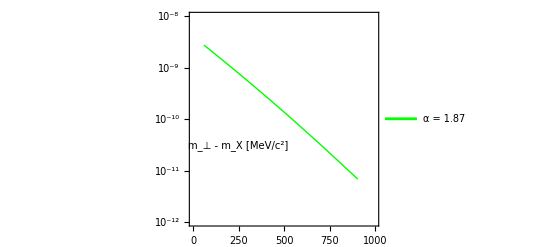

```mathematica
PlotMtHe3opt=ListLogPlot[MtHe3opt,PlotStyle->{Directive[Green,Thick]},PlotRange->{{0,1000},{10^-12,10^-8}},Axes->False,Frame->True,Joined->True,FrameStyle->Directive[Black,Thickness[0.005],14],Epilog->{Rotate[Text[Style["dN/(dy  SubsuperscriptBox[m, ⊥, 2] SubscriptBox[dm, ⊥]) [(MeV/c)^-3]",FontSize->10],{-180,Log[10^(-9)]}],90Degree],Text[Style["m_⊥ - m_X [MeV/c^2]",FontSize->10],{250,Log[3*10^(-11)]}]},PlotRangeClipping->False,ImagePadding->{{110,20},{50,20}},PlotLegends->Placed[{"α = 1.87"},{Right,Top}]]
```

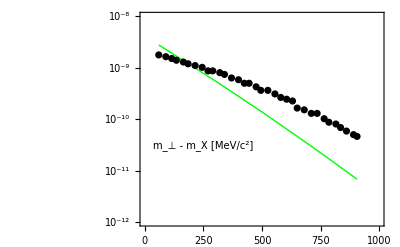

```mathematica
Show[{PlotMtHe3opt,He3ExpMt}]
```

#### Rapidity

```mathematica
rapHe3opt=Table[{rapHe3[[i,1]],rapHe3[[i,2]]*1.87},{i,1,13}]
```

{{-0.6,0.787823},{-0.5,1.48578},{-0.4,2.42552},{-0.3,3.48496},{-0.2,4.46819},{-0.1,5.16507},{0.,5.41694},{0.1,5.16507},{0.2,4.46819},{0.3,3.48496},{0.4,2.42552},{0.5,1.48578},{0.6,0.787823}}

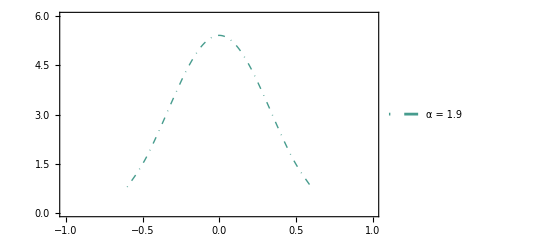

```mathematica
PlotRapHe3opt=ListPlot[rapHe3opt,PlotStyle->{Directive[RGBColor["#479C8E"],DotDashed,Thick]},PlotRange->{{-1,1},{0,6}},Axes->False,Frame->True,Joined->True,FrameStyle->Directive[Black,Thickness[0.005],14],Epilog->{Rotate[Text[Style["dN/dy",FontSize->12],{-1.2,3}],90Degree],Text[Style["y",FontSize->14],{0,-0.75}]},PlotRangeClipping->False,ImagePadding->{{50,10},{50,10}},PlotLegends->Placed[LineLegend[{"α = 1.9"},LegendMarkerSize->{30,16}],{Right,Top}],InterpolationOrder->2]
```

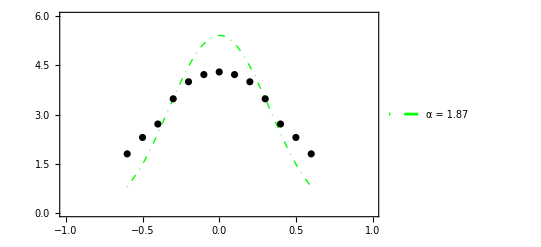

```mathematica
Show[{PlotRapHe3opt,ListPlot[He3Y,PlotStyle->Black,AxesLabel->{"m_t-m_0 [MeV]","1/((m^2)_t)dN/dm_t|_(y = 0) [MeV^-3]"},PlotLabel->"He3 distribution",PlotStyle->Thick,PlotStyle->Black]}]
```

## Spectra comparison

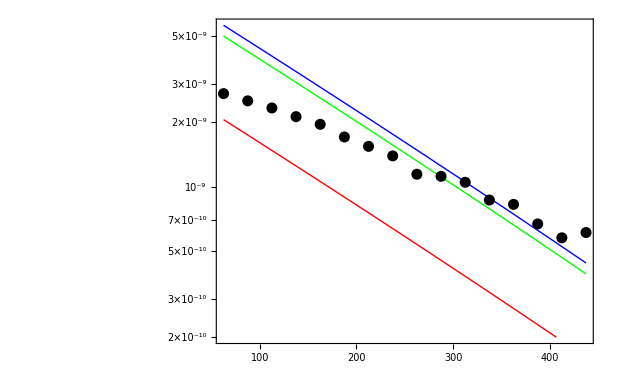

```mathematica
Show[{PlotTrytMt,PlotTrytMtResc,PlotTrytMtOpt,TrytExpMt},PlotRange->All]
```

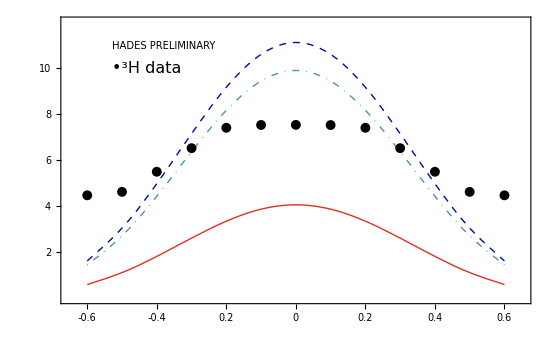

```mathematica
PlotRapH3 = Show[{PlotRapidityDistributionB,PlotrapH3resc,PlotrapH3opt,TrytExp},PlotRange->{{-0.65,0.65},{0,12}}]
```

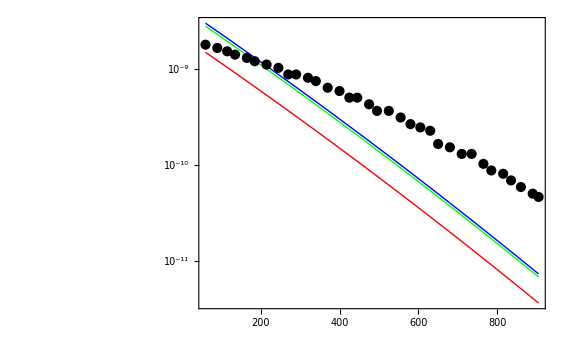

```mathematica
Show[{PlotHe3Mt,PlotHe3MtResc,PlotMtHe3opt,He3ExpMt},PlotRange->All]
```

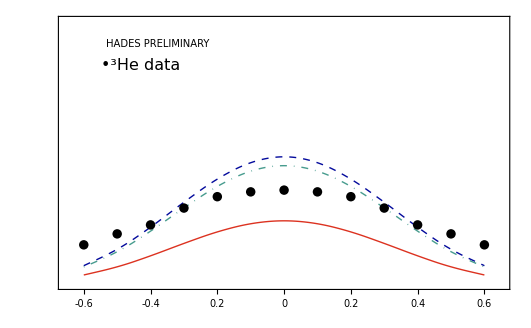

```mathematica
PlotRapHe3 = Show[{He3PlotRapidityDistributionB,PlotrapHe3resc,PlotRapHe3opt,He3Exp},PlotRange->{{-0.65,0.65},{0,12}}]
```

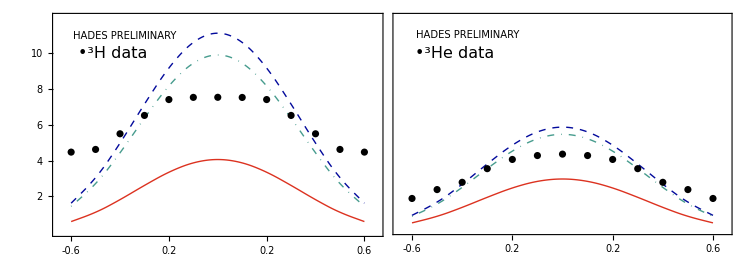

```mathematica
GraphicsGrid[{{PlotRapH3,PlotRapHe3}},Spacings->-45]
```

## Yields

```mathematica
(*H3 yield from the model*)
```

```mathematica
Sum[rapH3[[i,2]]*0.1,{i,1,13}]+1/2 Sum[(rapH3[[i-1,2]]-rapH3[[i,2]])^2*0.01,{i,2,13}]+1/2(rapH3[[1,2]]-rapH3[[2,2]])^2*0.01
```

3.10278

```mathematica
(*H3 yield from the rescalling to the experimental yield*)
```

```mathematica
Sum[rapH3[[i,2]]*0.1*2.74,{i,1,13}]+1/2 Sum[(rapH3[[i-1,2]]-rapH3[[i,2]])^2*0.01*2.74,{i,2,13}]+1/2(rapH3[[1,2]]-rapH3[[2,2]])^2*0.01*2.74
```

8.50163

```mathematica
(*H3 yield from the rescalling to the best fit*)
```

```mathematica
Sum[rapH3[[i,2]]*0.1*2.26,{i,1,13}]+1/2 Sum[(rapH3[[i-1,2]]-rapH3[[i,2]])^2*0.01*2.44,{i,2,13}]+1/2(rapH3[[1,2]]-rapH3[[2,2]])^2*0.01*2.44
```

7.0166

```mathematica
(*He3 yield from the model*)
```

```mathematica
Sum[rapHe3[[i,2]]*0.1,{i,1,13}]+1/2 Sum[(rapHe3[[i-1,2]]-rapHe3[[i,2]])^2*0.01,{i,2,13}]+1/2(rapHe3[[1,2]]-rapHe3[[2,2]])^2*0.01
```

2.20743

```mathematica
(*He3 yield from the rescalling to the experimental yield*)
```

```mathematica
Sum[rapHe3[[i,2]]*0.1*2.01,{i,1,13}]+1/2 Sum[(rapHe3[[i-1,2]]-rapHe3[[i,2]])^2*0.01*2.01,{i,2,13}]+1/2(rapHe3[[1,2]]-rapHe3[[2,2]])^2*0.01*2.01
```

4.43694

```mathematica
(*He3 yield from the rescalling to the best fit*)
```

```mathematica
Sum[rapHe3[[i,2]]*0.1*1.7,{i,1,13}]+1/2 Sum[(rapHe3[[i-1,2]]-rapHe3[[i,2]])^2*0.01*1.87,{i,2,13}]+1/2(rapHe3[[1,2]]-rapHe3[[2,2]])^2*0.01*1.87
```

3.75471